## Homework #1 Edwin Marcelo Vásconez López

Hubble Law

```mathematica
Clear ["Global`*"]
```

```mathematica
tA = SessionTime[];
c1 = UnitConvert[Quantity[1,"SpeedOfLight"]][[1]]
```

299792458

```mathematica
galaxylist = Import[
"/media/edwin/Datos/Yachay/Yachay 8 semestre/Cosmo/Homeworks/Homework 1/GalaxyList.csv"];
galaxycopy = galaxylist;
galaxylist[[1]]
numline = Length[galaxylist]
vgc := Table[galaxylist[[ii,7]] + 220 
N[Cos[(galaxylist[[ii,5]]-90)°]Cos[galaxylist[[ii,6]]°]],{ii,2,numline}]
```

{Galaxy Name,Type (RC3),err,D,GLON,GLAT,Vgsr (RC3),wts}

4040

#### Here we make a new list without a header to hold the revised data. The Header is {Galaxy Name, Type (RC3),wt.,D,GLON,GLAT,Vgc}

```mathematica
vgc = Table[galaxylist[[ii,7]] + 220N[Cos[(galaxylist[[ii,5]]-90)°]Cos[galaxylist[[ii,6]]°]],{ii,2,numline}];
galaxylistR = Table[{galaxycopy[[ii,1]],galaxycopy[[ii,2]],galaxycopy[[ii,8]],galaxycopy[[ii,4]],galaxycopy[[ii,5]],galaxycopy[[ii,6]],vgc[[ii-1]]},{ii,2,numline}];
datalist = Table[{galaxylistR[[ii,4]],vgc[[ii]]},{ii,1,numline-1}];
wtlist = Table[galaxylistR[[ii,3]],{ii,1,numline-1}];
```

#### The Velocity Versus Distance Relationship

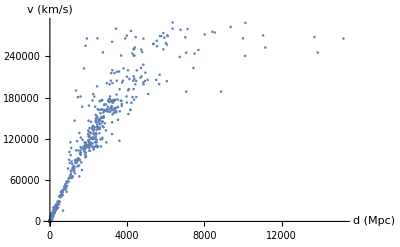

```mathematica
ListPlot[datalist, PlotRange->All, AxesLabel->{"d (Mpc)","v (km/s)"}]
```

#### The Special Relativistic Doppler Effect z for optical observations is defined as a difference of wavelength to rest wavelength ratio.

```mathematica
νobsR:= (√(c-v)νE)/(√(c-v))
λobs:=(√(c+v))/(√(c-v))λrest
zee:=FullSimplify[(λobs-λrest)/λrest]
```

#### For computation we put zee into a function to be able to put in v in km/s

```mathematica
c2 = N[c1/1000]
zeeobs[v1_]:=zee/.{c->c2,v->v1};
```

299792.

#### Thus we build and plot a new database list this time using z instead of Doppler velocity.

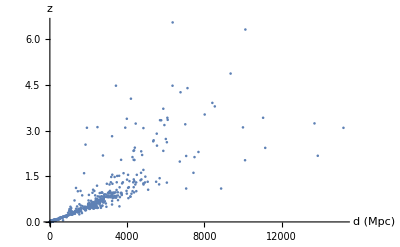

```mathematica
datalistA:=Table[{galaxylistR[[ii,4]],zeeobs[vgc[[ii]]]},{ii,1,numline-1}]
dataplot = ListPlot[datalistA,PlotRange->All,AxesLabel->{"d (Mpc)","z"}]
```

#### Data Fits for the NED Data (2009) using z versus Distance.

```mathematica
lmw3 = LinearModelFit[datalistA,{d,d^2},d,Weights->wtlist^2,IncludeConstantBasis->False]
```

FittedModel[0.000248559 d+8.19375×10^-9 d^2]

#### Computable expression for plotting

```mathematica
eqw3 = Normal[lmw3]
```

0.000248559 d+8.19375×10^-9 d^2

#### Fit Coefficients

```mathematica
coeff3 = lmw3["BestFitParameters"]
```

{0.000248559,8.19375×10^-9}

#### Coefficient Errors

```mathematica
coefe3 = lmw3["ParameterErrors"]
```

{1.37397×10^-6,4.89558×10^-10}

#### Correlation Coefficient of fit

```mathematica
ccoef3=√lmw3["RSquared"]
```

0.979642

#### Fit Errors in Standard Units (km/s/megaparsec)

```mathematica
coefe3 c2
```

{0.411905,0.000146766}

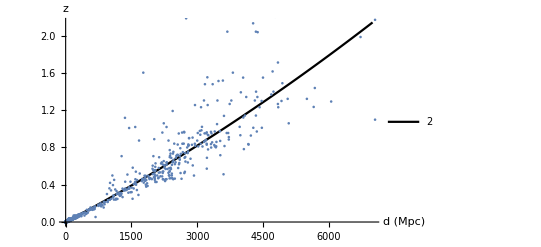

```mathematica
tplot3:=Plot[eqw3/.d->d1,{d1,0,7000},AxesLabel->{"d (Mpc)","z"},PlotLegends->{"2"},PlotStyle->Black]
Show[{tplot3,dataplot}]
```

#### Play “what if” with the exponents of the weights

```mathematica
lmw4 = LinearModelFit[datalistA,{d,d^2},d,Weights->wtlist^2.8,IncludeConstantBasis->False]
eqw4 = Normal[lmw4]
coeff4 = lmw4["BestFitParameters"]
coefe4 = lmw4["ParameterErrors"]
ccoef4=√lmw4["RSquared"]
coefe4 c2
tplot4:=Plot[eqw4/.d->d1,{d1,0,7000},AxesLabel->{"d (Mpc)","z"},PlotStyle->Blue,PlotLegends->{"2.8"}]
```

FittedModel[0.000242154 d+9.91612×10^-9 d^2]

0.000242154 d+9.91612×10^-9 d^2

{0.000242154,9.91612×10^-9}

{8.47757×10^-7,4.94321×10^-10}

0.996349

{0.254151,0.000148194}

```mathematica
lmw5 = LinearModelFit[datalistA,{d,d^2},d,Weights->wtlist^-0.75,IncludeConstantBasis->False]
eqw5 = Normal[lmw5]
coeff5 = lmw5["BestFitParameters"]
coefe5 = lmw5["ParameterErrors"]
ccoef5=√lmw5["RSquared"]
coefe5 c2
tplot5:=Plot[eqw5/.d->d1,{d1,0,7000},AxesLabel->{"d (Mpc)","z"},PlotStyle->Red,PlotLegends->{"-0.75"}]
```

FittedModel[0.000475419 d-1.58258×10^-8 d^2]

0.000475419 d-1.58258×10^-8 d^2

{0.000475419,-1.58258×10^-8}

{6.29528×10^-6,7.64×10^-10}

0.889588

{1.88728,0.000229041}

```mathematica
lmw6 = LinearModelFit[datalistA,{d,d^2},d,Weights->wtlist^(7/2),IncludeConstantBasis->False]
eqw6 = Normal[lmw6]
coeff6 = lmw6["BestFitParameters"]
coefe6 = lmw6["ParameterErrors"]
ccoef6=√lmw6["RSquared"]
coefe6 c2
tplot6:=Plot[eqw6/.d->d1,{d1,0,7000},AxesLabel->{"d (Mpc)","z"},PlotStyle->Green,PlotLegends->{"3.5"}]
```

FittedModel[0.000240346 d+1.0678×10^-8 d^2]

0.000240346 d+1.0678×10^-8 d^2

{0.000240346,1.0678×10^-8}

{8.98137×10^-7,6.1408×10^-10}

0.99844

{0.269255,0.000184096}

```mathematica
lmw7 = LinearModelFit[datalistA,{d,d^2},d,Weights->wtlist^5.75,IncludeConstantBasis->False]
eqw7 = Normal[lmw7]
coeff7 = lmw7["BestFitParameters"]
coefe7 = lmw7["ParameterErrors"]
ccoef7=√lmw7["RSquared"]
coefe7 c2
tplot7:=Plot[eqw7/.d->d1,{d1,0,7000},AxesLabel->{"d (Mpc)","z"},PlotStyle->Yellow,PlotLegends->{"5.75"}]
```

FittedModel[0.000260757 d-5.53437×10^-9 d^2]

0.000260757 d-5.53437×10^-9 d^2

{0.000260757,-5.53437×10^-9}

{1.41801×10^-6,1.06155×10^-9}

0.999159

{0.425108,0.000318245}

```mathematica
lmw8 = LinearModelFit[datalistA,{d,d^2},d,Weights->wtlist^0.045,IncludeConstantBasis->False]
eqw8 = Normal[lmw8]
coeff8 = lmw8["BestFitParameters"]
coefe8 = lmw8["ParameterErrors"]
ccoef8=√lmw8["RSquared"]
coefe8 c2
tplot8:=Plot[eqw8/.d->d1,{d1,0,7000},AxesLabel->{"d (Mpc)","z"},PlotStyle->Orange,PlotLegends->{"0.045"}]
```

FittedModel[0.000382425 d-6.52405×10^-9 d^2]

0.000382425 d-6.52405×10^-9 d^2

{0.000382425,-6.52405×10^-9}

{5.23508×10^-6,7.03033×10^-10}

0.892214

{1.56944,0.000210764}

```mathematica
lmw9 = LinearModelFit[datalistA,{d,d^2},d,Weights->wtlist^4.37,IncludeConstantBasis->False]
eqw9 = Normal[lmw9]
coeff9 = lmw9["BestFitParameters"]
coefe9 = lmw9["ParameterErrors"]
ccoef9=√lmw9["RSquared"]
coefe9 c2
tplot9:=Plot[eqw9/.d->d1,{d1,0,7000},AxesLabel->{"d (Mpc)","z"},PlotStyle->Purple,PlotLegends->{"4.37"}]
```

FittedModel[0.000245118 d+6.74555×10^-9 d^2]

0.000245118 d+6.74555×10^-9 d^2

{0.000245118,6.74555×10^-9}

{1.13836×10^-6,8.29301×10^-10}

0.998882

{0.341272,0.000248618}

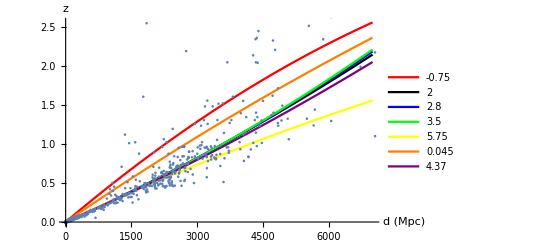

```mathematica
Show[{tplot5,tplot3,tplot4,tplot6,tplot7,tplot8,tplot9,dataplot}]
```

#### Continue playing

```mathematica
lmw4n = LinearModelFit[datalistA,{d,d^2.8},d,Weights->wtlist^2.8,IncludeConstantBasis->False]
eqw4n = Normal[lmw4n]
coeff4n = lmw4n["BestFitParameters"]
coefe4n = lmw4n["ParameterErrors"]
ccoef4n=√lmw4n["RSquared"]
coefe4n c2
tplot4n:=Plot[eqw4n/.d->d1,{d1,0,7000},AxesLabel->{"d (Mpc)","z"},PlotStyle->Blue,PlotLegends->{"2.8"}]
```

FittedModel[0.000255276 d+3.76082×10^-12 d^2.8]

0.000255276 d+3.76082×10^-12 d^2.8

{0.000255276,3.76082×10^-12}

{4.1235×10^-7,3.20714×10^-13}

0.996116

{0.123619,9.61476×10^-8}

```mathematica
lmw5n = LinearModelFit[datalistA,{d,d^-0.75},d,Weights->wtlist^-0.75,IncludeConstantBasis->False]
eqw5n = Normal[lmw5n]
coeff5n = lmw5n["BestFitParameters"]
coefe5n = lmw5n["ParameterErrors"]
ccoef5n=√lmw5n["RSquared"]
coefe5n c2
tplot5n:=Plot[eqw5n/.d->d1,{d1,0,7000},AxesLabel->{"d (Mpc)","z"},PlotStyle->Red,PlotLegends->{"-0.75"}]
```

FittedModel[-0.000236459/d^0.75+0.000360253 d]

-0.000236459/d^0.75+0.000360253 d

{0.000360253,-0.000236459}

{3.10589×10^-6,0.00506726}

0.877036

{0.931124,1519.13}

```mathematica
lmw6n = LinearModelFit[datalistA,{d,d^(7/2)},d,Weights->wtlist^(7/2),IncludeConstantBasis->False]
eqw6n = Normal[lmw6n]
coeff6n = lmw6n["BestFitParameters"]
coefe6n = lmw6n["ParameterErrors"]
ccoef6n=√lmw6n["RSquared"]
coefe6n c2
tplot6n:=Plot[eqw6n/.d->d1,{d1,0,7000},AxesLabel->{"d (Mpc)","z"},PlotStyle->Green,PlotLegends->{"3.5"}]
```

FittedModel[0.000255038 d+4.92381×10^-15 d^(7/2)]

0.000255038 d+4.92381×10^-15 d^(7/2)

{0.000255038,4.92381×10^-15}

{2.44335×10^-7,8.73846×10^-16}

0.998336

{0.0732499,2.61972×10^-10}

```mathematica
lmw7n = LinearModelFit[datalistA,{d,d^5.75},d,Weights->wtlist^5.75,IncludeConstantBasis->False]
eqw7n = Normal[lmw7n]
coeff7n = lmw7n["BestFitParameters"]
coefe7n = lmw7n["ParameterErrors"]
ccoef7n=√lmw7n["RSquared"]
coefe7n c2
tplot7n:=Plot[eqw7n/.d->d1,{d1,0,7000},AxesLabel->{"d (Mpc)","z"},PlotStyle->Yellow,PlotLegends->{"5.75"}]
```

FittedModel[0.000253412 d+1.60963×10^-24 d^5.75]

0.000253412 d+1.60963×10^-24 d^5.75

{0.000253412,1.60963×10^-24}

{1.64564×10^-7,1.4316×10^-23}

0.999154

{0.049335,4.29182×10^-18}

```mathematica
lmw8n = LinearModelFit[datalistA,{d,d^0.045},d,Weights->wtlist^0.045,IncludeConstantBasis->False]
eqw8n = Normal[lmw8n]
coeff8n = lmw8n["BestFitParameters"]
coefe8n = lmw8n["ParameterErrors"]
ccoef8n=√lmw8n["RSquared"]
coefe8n c2
tplot8n:=Plot[eqw8n/.d->d1,{d1,0,7000},AxesLabel->{"d (Mpc)","z"},PlotStyle->Orange,PlotLegends->{"0.045"}]
```

FittedModel[-0.00537653 d^0.045+0.000342872 d]

-0.00537653 d^0.045+0.000342872 d

{0.000342872,-0.00537653}

{2.93021×10^-6,0.00280095}

0.889879

{0.878455,839.703}

```mathematica
lmw9n = LinearModelFit[datalistA,{d,d^4.37},d,Weights->wtlist^4.37,IncludeConstantBasis->False]
eqw9n = Normal[lmw9n]
coeff9n = lmw9n["BestFitParameters"]
coefe9n = lmw9n["ParameterErrors"]
ccoef9n=√lmw9n["RSquared"]
coefe9n c2
tplot9n:=Plot[eqw9n/.d->d1,{d1,0,7000},AxesLabel->{"d (Mpc)","z"},PlotStyle->Purple,PlotLegends->{"4.37"}]
```

FittedModel[0.000254191 d+1.39428×10^-18 d^4.37]

0.000254191 d+1.39428×10^-18 d^4.37

{0.000254191,1.39428×10^-18}

{1.93682×10^-7,8.06262×10^-19}

0.998864

{0.0580645,2.41711×10^-13}

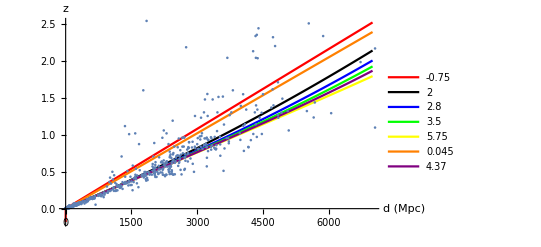

```mathematica
Show[{tplot5n,tplot3,tplot4n,tplot6n,tplot7n,tplot8n,tplot9n,dataplot}]
```